```mathematica
p=√((ϵ^2-m^2 c^4)/c^2)
dp=D[p,ϵ]
f[ϵ_]=(g 4π)/h^3(Exp[(ϵ-ϵF)/(k T)]+1)^-1 p^2 dp //PowerExpand//FullSimplify
Integrate[(1/(3m))p^2 f[ϵ],{ϵ,0,ϵF},Assumptions->{m>0 && c>0 && h>0 && g>0&&ϵF>0 && k>0 &&T>0 && ϵ<ϵF}] //PowerExpand //FullSimplify
```

√((-c^4 m^2+ϵ^2)/c^2)

ϵ/(c^2 √((-c^4 m^2+ϵ^2)/c^2))

(4 g π ϵ √(-c^4 m^2+ϵ^2))/(c^3 (1+ⅇ^((ϵ-ϵF)/(k T))) h^3)

Integrate[(4 g π ϵ (-c^4 m^2+ϵ^2)^(3/2))/(3 c^5 (1+ⅇ^((ϵ-ϵF)/(k T))) h^3 m),{ϵ,0,ϵF},Assumptions→m>0&&c>0&&h>0&&g>0&&ϵF>0&&k>0&&T>0&&ϵ<ϵF]

Problem 2.e : Blackbody at 300 K

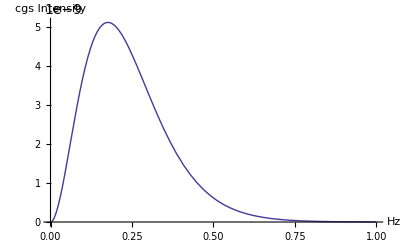

hν_max = 1.16863×10^-13

k(T=300) = 4.14195×10^-14

hν_max= 2.82144 kT

Problem 2.f : Blackbody at 300 K

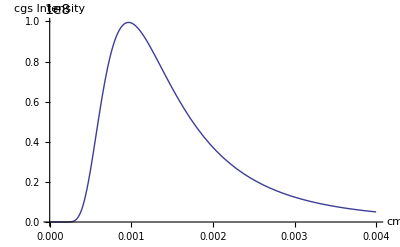

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

λ_max = 0.000965924

λ_max*(T=300)=0.289777

∫_0^∞ f[ν]ⅆνⅆΩ = (16 k^3 π T^3 Zeta[3])/(c^3 h^3)

n = 20.2868 T^3

20.2868 T^3

Problem 2.e : Blackbody at 300 K

-Graphics-

hν_max = 1.16863×10^-13

k(T=300) = 4.14195×10^-14

hν_max= 2.82144 kT

Problem 2.f : Blackbody at 300 K

-Graphics-

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

λ_max = 0.000965924

λ_max*(T=300)=0.289777

```mathematica
Remove["Global`*"]
n[ν_]=(2  ν^2)/c^3(Exp[h ν/(k T)]-1)^-1;

Work[x_]:=Integrate[x Sin[θ],{ν,0,∞},{ϕ,0,2π},{θ,0,π},Assumptions->{h>0&& c>0 && k>0 && T>0}]
u=Work[h ν n[ν]];
p=Work[h ν n[ν] Cos[θ]^2];
B[ν_,T_]=c h ν n[ν];
F=Integrate[B[ν,T]Cos[θ] Sin[θ],{ν,0,∞},{ϕ,0,2π},{θ,0,π/2},Assumptions->{h>0&& c>0 && k>0 && T>0}];
h=6.62606957*10^-27;
k=1.3806488*10^-16 ;
c=2.99792458*10^10;
h ν/.NMaximize[{B[ν,300],ν>10^13},ν][[2]];
k 300;
%%/%;
Print["Problem 2.e : Blackbody at 300 K"]
Plot[B[ν,T=300],{ν,10^9,10^14},AxesLabel->{"Hz","cgs Intensity"}]
Print["hν_max = ", %%%%%]
Print["k(T=300) = ", %%%%%]
Print["hν_max= ",%%%%%," kT"]
Print["Problem 2.f : Blackbody at 300 K"]
Plot[((2h c^2)/(λ^5(-1+ⅇ^(hc/(k λ 300))))),{λ,10*10^-6,40*10^-4},AxesLabel->{"cm","cgs Intensity"}]
NMaximize[{((2h c^2)/(λ^5(-1+ⅇ^(hc/(k λ 300))))),λ>.0001},λ];
Print["λ_max = ",λ/.%[[2]]]
Print["λ_max*(T=300)=",300*λ/.%%[[2]]]
Clear[h,k,c,T]
Print["∫_0^∞ f[ν]ⅆνⅆΩ = ",nd= Work[n[ν]]]
h=6.62606957*10^-27;
k=1.3806488*10^-16 ;
c=2.99792458*10^10;
Print["n = ",nd]
```

```mathematica
Integrate[x^2/(Exp[x]-1),{x,0,∞}] //N
```

2.40411

```mathematica
2*π*1.38*10^-16*10^10 * 10^-18
```

8.6708×10^-24

```mathematica
((2h c^2)/(λ^5(-1+ⅇ^(hc/(k λ 300)))))/.λ->(k T x/(h c))^-1
```

(2 k^5 T^5 x^5)/(c^3 (-1+ⅇ^((T x)/300)) h^4)

```mathematica
D[x^5/(-1+ⅇ^x),x]==0 
NSolve[%]
```

(5 x^4)/(-1+ⅇ^x)-(ⅇ^x x^5)/((-1+ⅇ^x)^2)==0

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→4.96511}}